```mathematica
raw=Import[FileNameJoin[{NotebookDirectory[], "data","rb_continuous_contracts.csv"}]]
```

{{Date,close,settle,vwap,trade_hiscode},{2010/4/26,4734,4741,4741.29,RB1010.SHF},{2010/4/27,4678,4689,4689.71,RB1010.SHF},{2010/4/28,4588,4619,4619.75,RB1010.SHF},{2010/4/29,4583,4599,4599.17,RB1010.SHF},{2010/4/30,4635,4609,4609.64,RB1010.SHF},{2010/5/4,4665,4649,4649.36,RB1010.SHF},{2010/5/5,4653,4636,4636.11,RB1010.SHF},{2010/5/6,4637,4653,4653.01,RB1010.SHF},2676,{2021/5/13,5915,6000,6000.3,RB2110.SHF},{2021/5/14,5641,5761,5761.04,RB2110.SHF},{2021/5/17,5596,5620,5620.76,RB2110.SHF},{2021/5/18,5610,5621,5621.11,RB2110.SHF},{2021/5/19,5309,5444,5444.51,RB2110.SHF},{2021/5/20,5186,5150,5150.21,RB2110.SHF},{2021/5/21,5112,5158,5158.58,RB2110.SHF},{2021/5/24,5112,5158,,RB2110.SHF}}
 |  |  |  |

```mathematica
raw[[2]]
```

{2010/4/26,4734,4741,4741.29,RB1010.SHF}

```mathematica
price=TimeSeries[Part[Transpose[Drop[raw, 1]],{1,2}]//N//Transpose]
```

TimeSeries[…]

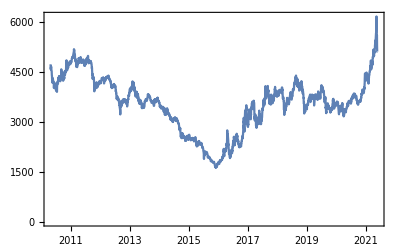

```mathematica
DateListPlot[price]
```

```mathematica
mat=Part[Transpose[Drop[raw, 1]],{1,2,-1}]//Transpose
```

{{2010/4/26,4734,RB1010.SHF},{2010/4/27,4678,RB1010.SHF},{2010/4/28,4588,RB1010.SHF},{2010/4/29,4583,RB1010.SHF},{2010/4/30,4635,RB1010.SHF},{2010/5/4,4665,RB1010.SHF},{2010/5/5,4653,RB1010.SHF},{2010/5/6,4637,RB1010.SHF},{2010/5/7,4545,RB1010.SHF},{2010/5/10,4534,RB1010.SHF},{2010/5/11,4479,RB1010.SHF},{2010/5/12,4406,RB1010.SHF},{2010/5/13,4400,RB1010.SHF},2666,{2021/5/6,5665,RB2110.SHF},{2021/5/7,5678,RB2110.SHF},{2021/5/10,6012,RB2110.SHF},{2021/5/11,6086,RB2110.SHF},{2021/5/12,6171,RB2110.SHF},{2021/5/13,5915,RB2110.SHF},{2021/5/14,5641,RB2110.SHF},{2021/5/17,5596,RB2110.SHF},{2021/5/18,5610,RB2110.SHF},{2021/5/19,5309,RB2110.SHF},{2021/5/20,5186,RB2110.SHF},{2021/5/21,5112,RB2110.SHF},{2021/5/24,5112,RB2110.SHF}}
 |  |  |  |

```mathematica
prvCode=Null;
Do[
curCode=mat⟦i,3⟧;
If[prvCode==Null,prvCode=curCode];
If[Not[prvCode==curCode],
ratio=N[mat⟦i,2⟧/mat⟦i-1,2⟧];
mat⟦1;;i-1,2⟧*=ratio;
prvCode=curCode],
{i,Length[mat]}]
```

```mathematica
mat
```

{{2010/4/26,3224.24,RB1010.SHF},{2010/4/27,3186.1,RB1010.SHF},{2010/4/28,3124.81,RB1010.SHF},{2010/4/29,3121.4,RB1010.SHF},{2010/4/30,3156.82,RB1010.SHF},{2010/5/4,3177.25,RB1010.SHF},{2010/5/5,3169.08,RB1010.SHF},{2010/5/6,3158.18,RB1010.SHF},{2010/5/7,3095.52,RB1010.SHF},{2010/5/10,3088.03,RB1010.SHF},{2010/5/11,3050.57,RB1010.SHF},2671,{2021/5/11,6086,RB2110.SHF},{2021/5/12,6171,RB2110.SHF},{2021/5/13,5915,RB2110.SHF},{2021/5/14,5641,RB2110.SHF},{2021/5/17,5596,RB2110.SHF},{2021/5/18,5610,RB2110.SHF},{2021/5/19,5309,RB2110.SHF},{2021/5/20,5186,RB2110.SHF},{2021/5/21,5112,RB2110.SHF},{2021/5/24,5112,RB2110.SHF}}
 |  |  |  |

```mathematica
price2=Part[Transpose[mat],{1,2}]//Transpose//TimeSeries
```

TimeSeries[…]

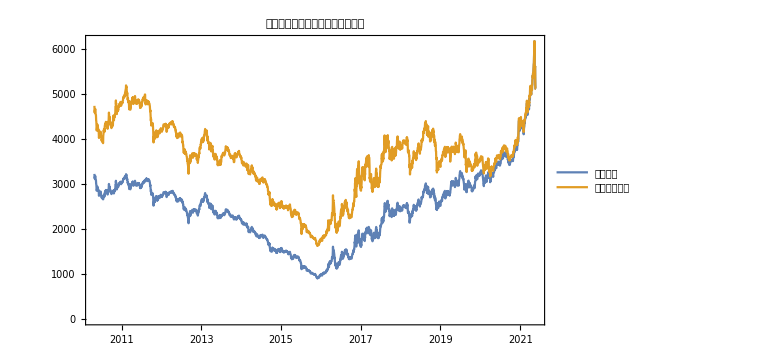

```mathematica
DateListPlot[{price2,price},
PlotLegends->Placed[{"平滑价格","原始价格序列"},{0.1,0.1}],
ImageSize->Large,PlotLabel->"上期所螺纹钢期货主力合约收盘价"]
```

```mathematica
mat[[1390]]
```

{2016/1/13,969.923,RB1605.SHF}

```mathematica
ret=Differences[N[Log@price2]]["ValueList"]//Flatten;
ret[[;;1390]]*=-1;
```

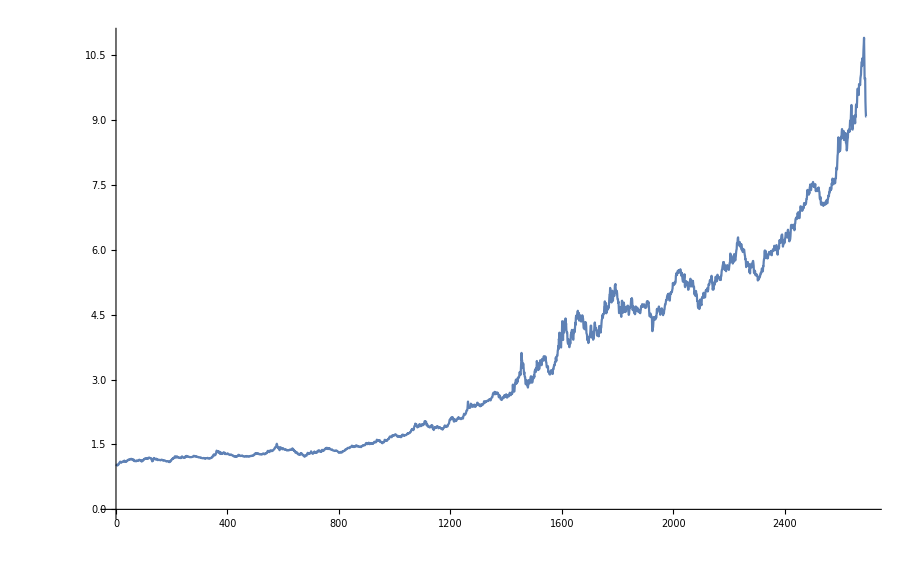

```mathematica
FoldList[#1*Exp[#2]&,1,ret]//ListLinePlot
```

```mathematica
acf[data_,lmax_,clev_:0.95]:=Show[ListPlot[CorrelationFunction[data,{0,lmax}],Filling->Axis,PlotRange->{{0,lmax},All},PlotStyle->PointSize[Medium]],
Graphics[{Dashed,Line[{{0,#},{lmax,#}}]}]&/@(Quantile[NormalDistribution[],{(1-clev)/2,1-(1-clev)/2}]/(√Length[data]))]
```

```mathematica
With[{p=Log@price2["ValueList"]//Flatten},
Animate[
Show[acf[Differences[p,1,d],300],PlotLabel-> ToString[d]<>"-Step Difference"],{d,1,30,1}]]
```

```mathematica
With[{p=Log@price2["ValueList"]//Flatten},
Animate[
Show[acf[N@Differences[p,1,d][[;;;;d]],30],PlotLabel-> ToString[d]<>"日收益率"],{d,1,30,1}]]
```

```mathematica
{1,2,3,4,5}[[;;;;2]]
```

{1,3,5}

```mathematica
With[{p=Log@price2["ValueList"]//Flatten},
Table[
UnitRootTest[Differences[p,1,d],Automatic,"ShortTestConclusion"]
,{d,1,30,1}]]
```

{Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject,Reject}

```mathematica
testM=With[{p=Log@price2["ValueList"]//Flatten},TimeSeriesModelFit[Differences[p,1,10],{"ARMA",{3,1}}]]
```

TimeSeriesModel[…]

```mathematica
testM["CandidateSelectionTable"]
```

| Candidate | AIC
1 | ARProcess[3] | -21103.7
2 | ARProcess[4] | -21102.1
3 | ARProcess[2] | -21092.2
4 | ARProcess[1] | -21092.1
5 | ARMAProcess[1,1] | -20988.1
6 | ARMAProcess[3,1] | -20981.9
7 | ARMAProcess[4,1] | -20948.8
8 | ARMAProcess[2,1] | -20903.8
9 | MAProcess[1] | -18702.
10 | MAProcess[0] | -16645.6

```mathematica
testM["FitResiduals"]//AutocorrelationTest[#,300,"ShortTestConclusion"]&
```

Reject

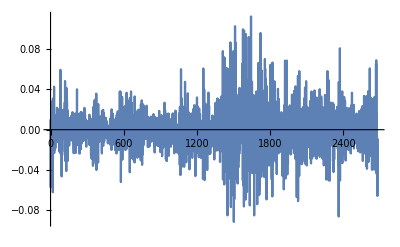

```mathematica
ListLinePlot[testM["FitResiduals"],PlotRange->All]
```

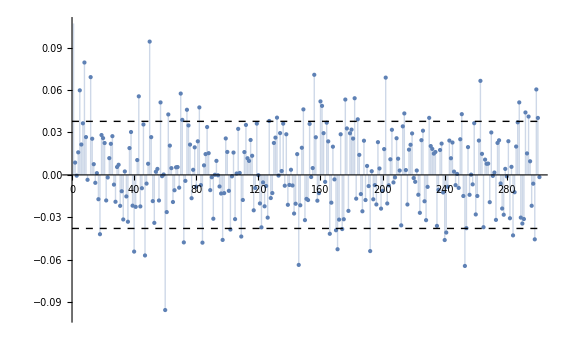

```mathematica
acf[testM["FitResiduals"]["ValueList"]//Flatten, 300,0.95]
```

```mathematica
%31["TemporalData"]
```

TemporalData[…]

```mathematica
%31[HoldComplete["BestFit"]]
```

TimeSeriesModel[…][HoldComplete[BestFit]]

```mathematica
Normal[%31]
```

ARProcess[0.000233811,{0.922747,0.0378959,-0.0709491},0.000381131]

```mathematica
Differences[{a,b,c,d,e,f,g,h,i,j,k,l,m,n},1,3]
```

{-a+d,-b+e,-c+f,-d+g,-e+h,-f+i,-g+j,-h+k,-i+l,-j+m,-k+n}

```mathematica
logret=Differences@Log@N@price;
logret2=N@Differences@Log@price2;
```

```mathematica
MovingMap[Mean,logret2,logret2["PathLength"],None]
```

TimeSeries[…]

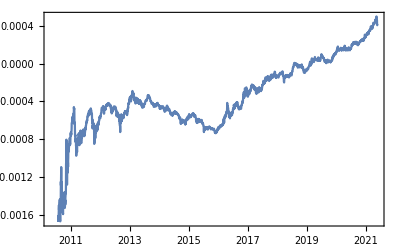

```mathematica
DateListPlot[%21]
```

Variance::shlen: The argument {-0.0118998} should have at least two elements.

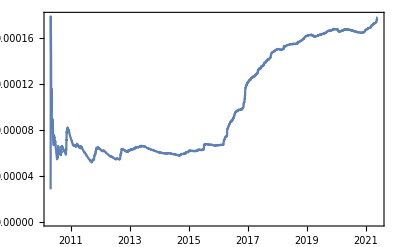

```mathematica
DateListPlot[%19]
```

```mathematica
logret2
```

TimeSeries[…]

Kurtosis::shlen: The argument {-0.0118998} should have at least two elements.

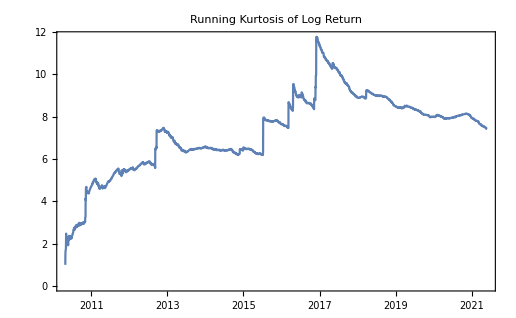

```mathematica
DateListPlot[%14,PlotLabel->"Running Kurtosis of Log Return"]
```

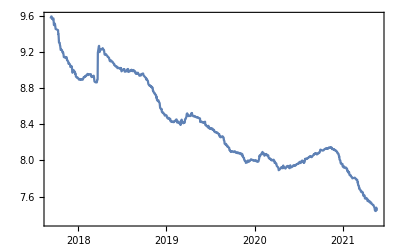

```mathematica
DateListPlot[%12]
```

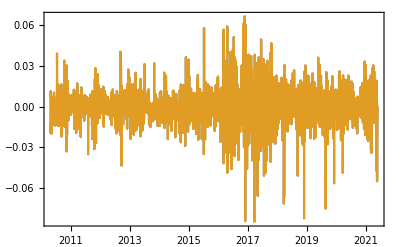

```mathematica
DateListPlot[{logret2, logret},PlotRange->All]
```

```mathematica
AutocorrelationTest[logret2["ValueList"]//Flatten,Automatic,"TestConclusion"]
```

The null hypothesis that the data are uncorrelated to lag 8 is rejected at the 5 percent level based on the Ljung-Box test.

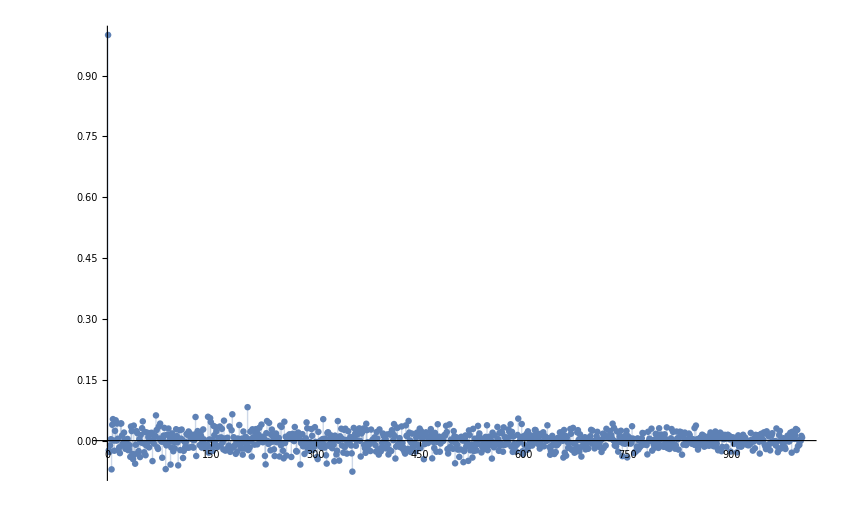

```mathematica
ListPlot[CorrelationFunction[logret["ValueList"]//Flatten,{1000}],Filling->Axis,PlotRange->All]
```

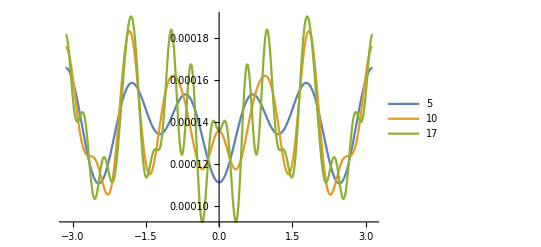

```mathematica
cutoffs={5,10,17};
spec=Table[PowerSpectralDensity[logret2["ValueList"]//Flatten,ω,i],{i,cutoffs}];
Plot[Evaluate@spec,{ω,-π,π},PlotLegends->cutoffs]
```

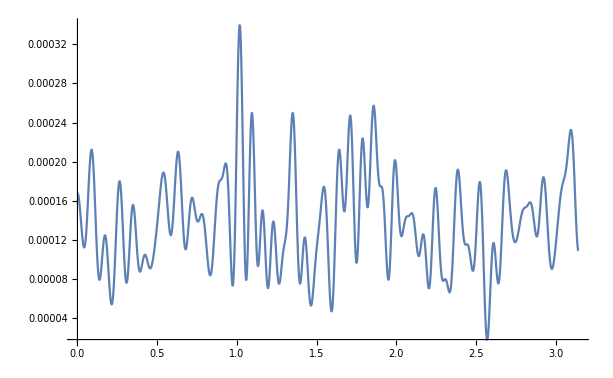

```mathematica
Plot[Evaluate@PowerSpectralDensity[logret2["ValueList"]//Flatten,ω,100],{ω,0,π}]
```

```mathematica
PowerSpectralDensity[logret["ValueList"]//Flatten,100]
```

0.000572188

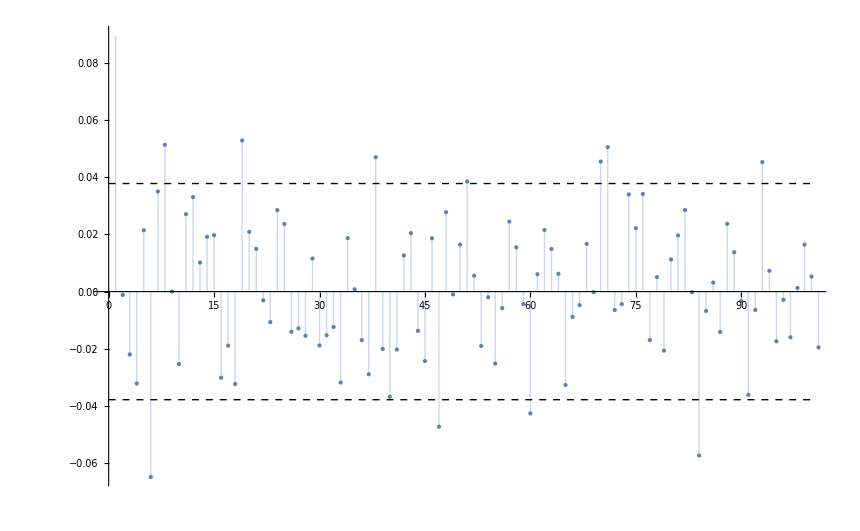

```mathematica
acf[logret2["ValueList"]//Flatten, 100,.95]
```

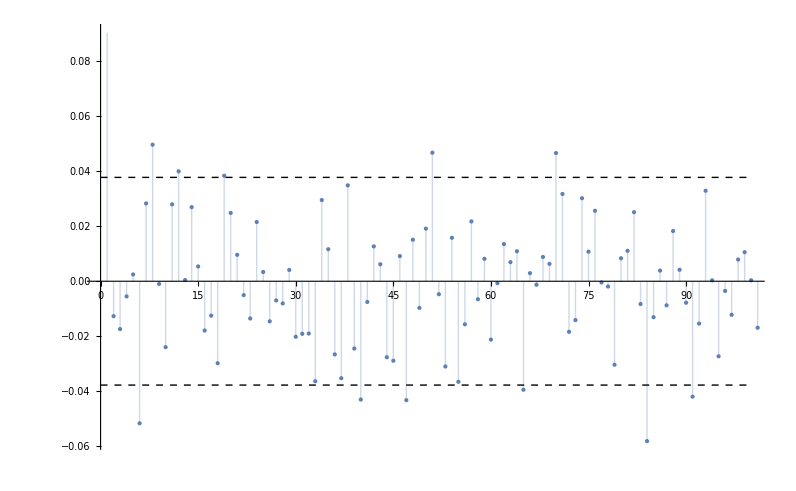

```mathematica
acf[logret["ValueList"]//Flatten, 100,.95]
```

```mathematica
TimeSeriesModelFit[logret2["ValueList"]//Flatten,"ARMA"]
```

TimeSeriesModel[…]

```mathematica
%64["TemporalData"]
```

TemporalData[…]

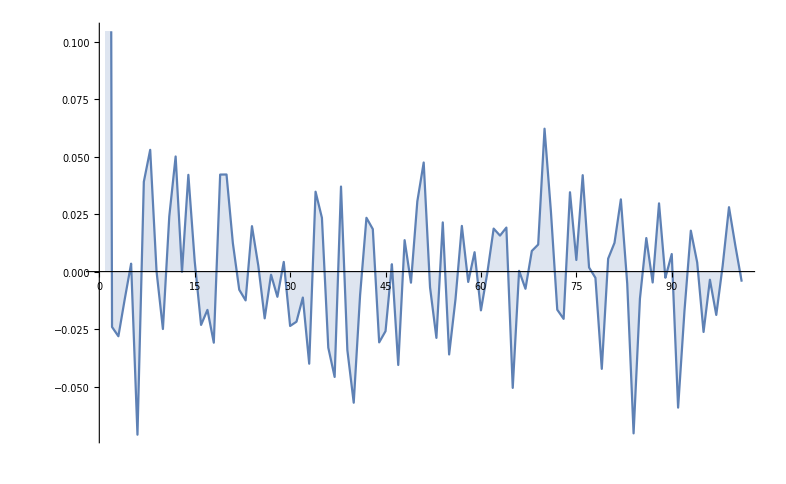

```mathematica
ListLinePlot[CorrelationFunction[logret["ValueList"]//Flatten,{100}],Filling->Axis,PlotRange->Automatic]
```

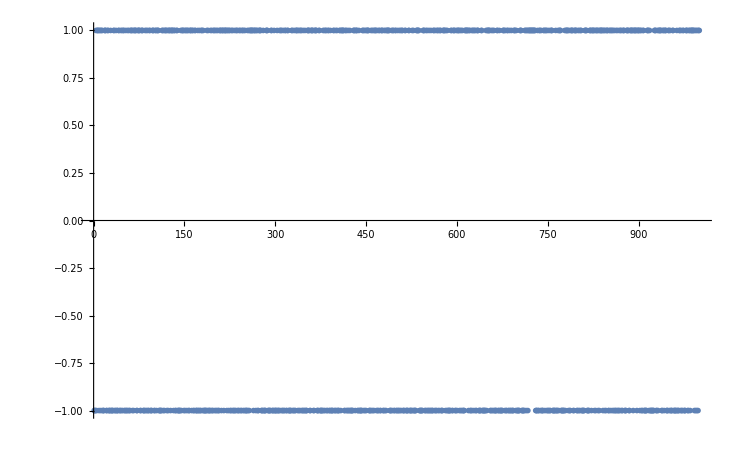

```mathematica
Drop[CorrelationFunction[logret["ValueList"]//Flatten,{1000}],1]//Sign//ListPlot
```

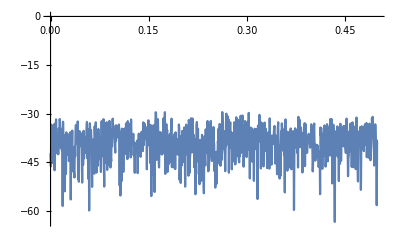

```mathematica
Periodogram[logret["ValueList"]//Flatten](*//MovingAverage[#,{Length[#]}]&//ListLinePlot*)
```

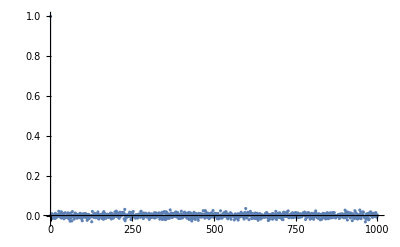

```mathematica
ListPlot[CorrelationFunction[RandomFunction[WhiteNoiseProcess[2],{10000}],{1000}],Filling->Axis,PlotRange->All]
```

```mathematica
TimeSeriesModelFit[logret["ValueList"]]
```

TimeSeriesModel[…]

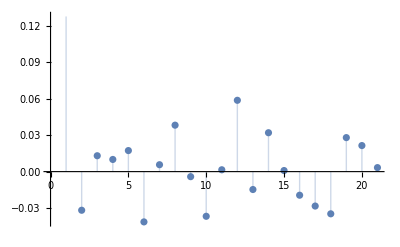

```mathematica
ListPlot[CorrelationFunction[logret["ValueList"]//Flatten,{20}],Filling->Axis]
```

```mathematica
%264["ParameterTable"]
```

General::munfl: 3.63264613726112145023568×10^-401 is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
α_1 | 0.0620456 | 0.00846164 | 7.33257 | 1.70616×10^-13
β_1 | 0.915493 | 0.0161534 | 56.6751 | 0.

```mathematica
%264["TemporalData"]
```

TemporalData[…]

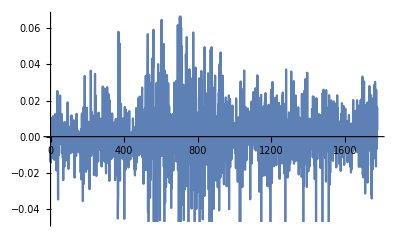

```mathematica
ListLinePlot[%266]
```

```mathematica
Normal[%264]
```

GARCHProcess[6.1871×10^-6,{0.0620456},{0.915493}]

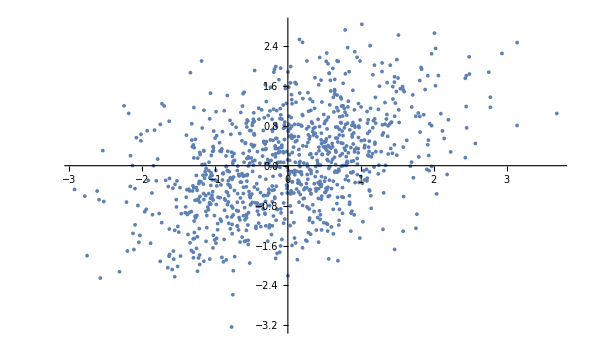

```mathematica
ListPlot[RandomVariate[BinormalDistribution[0.444],{1000}]]
```